```mathematica
Get["lqrw.m", Path -> {"f:\\MSc"}]
BitOrder=3;
σ=ⅇ^((π 2 ⅈ)/BitOrder);
({{a, b, c}, {d, e, f}, {g, h, i}})=H=({{1, 1, 1}, {1, σ^(BitOrder-1), σ}, {1, σ, σ^(BitOrder-1)}})/(√BitOrder);
Test=Normal[SparseArray[{
{1,1}->a1,
{1,2}->b1,
{1,3}->c1,
{2,1}->a2,
{2,2}->b2,
{2,3}->c2,
{3,1}->a3,
{3,2}->b3,
{3,3}->c3,
{4,1}->a4,
{4,2}->b4,
{4,3}->c4
}]];
Test = Normal[SparseArray[{
{4,3}->0,
{1,1}->1
}]]
```

(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
StatesToPositionalProbabilites[SingleLazyItteration[Test,H]]
Simplify[StatesToPositionalProbabilites[MultipleLazySteps[Test,H,10]]]
```

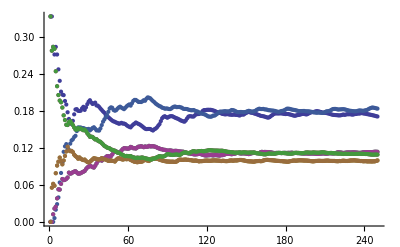

```mathematica
ListPlot[Transpose[CumulativeMean[StatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{8,3}->0,
{1,1}->1
}]]
,H,250]]]]
```

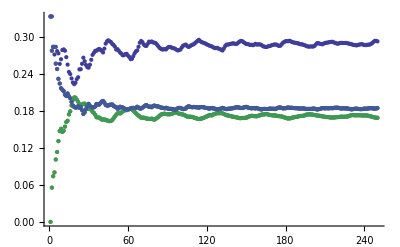

```mathematica
ListPlot[Transpose[CumulativeMean[StatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{5,3}->0,
{1,1}->1
}]]
,H,250]]]]
```

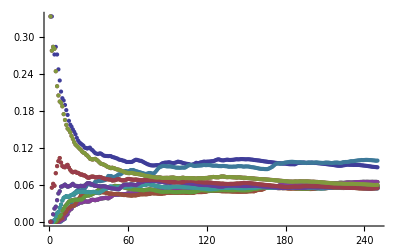

```mathematica
ListPlot[Transpose[CumulativeMean[StatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{16,3}->0,
{1,1}->1
}]]
,H,250]]]]
```

```mathematica
UpTo16Nodes2000Steps=Table[
CumulativeMean[StatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{v,3}->0,
{1,1}->1
}]]
,H,2000]],
{v,Range[16]}];
```

```mathematica
Transpose[Table[N[Take[UpTo10Nodes100Steps[[v]],-1]],{v,Range[10]}]]
```

({1.} | {0.499806,0.500194} | {0.44,0.28,0.28} | {0.295065,0.195167,0.314601,0.195167} | {0.279799,0.184843,0.175257,0.175257,0.184843} | {0.219524,0.136209,0.138299,0.23146,0.138299,0.136209} | {0.216387,0.144407,0.121052,0.126348,0.126348,0.121052,0.144407} | {0.164854,0.109312,0.101085,0.114226,0.185901,0.114226,0.101085,0.109312} | {0.15735,0.108814,0.0977045,0.10262,0.112186,0.112186,0.10262,0.0977045,0.108814} | {0.134377,0.0889039,0.0804857,0.0858994,0.0994989,0.156047,0.0994989,0.0858994,0.0804857,0.0889039})

```mathematica
MatrixForm[Table[N[Mean/@Transpose[Take[UpTo10Nodes100Steps[[v]],-15]]],{v,Range[10]}]]
```

({1.}
{0.495235,0.504765}
{0.438913,0.280543,0.280543}
{0.30272,0.196063,0.305154,0.196063}
{0.280899,0.18388,0.175671,0.175671,0.18388}
{0.217597,0.137178,0.138697,0.230653,0.138697,0.137178}
{0.218251,0.145231,0.122702,0.122942,0.122942,0.122702,0.145231}
{0.169277,0.108564,0.0985886,0.115645,0.185128,0.115645,0.0985886,0.108564}
{0.161469,0.110446,0.0974611,0.10011,0.111248,0.111248,0.10011,0.0974611,0.110446}
{0.133153,0.0906172,0.0825698,0.0861099,0.0973914,0.153471,0.0973914,0.0861099,0.0825698,0.0906172})

```mathematica
UpTo16Nodes2000Steps>>"F:\MSc\UpTo16Nodes2000Steps.txt"
```

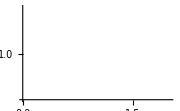
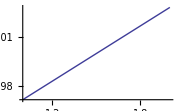
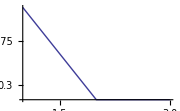
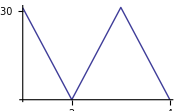
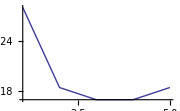
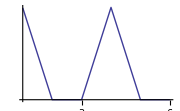
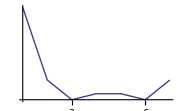
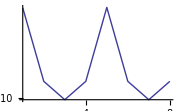

```mathematica
Table[
ListLogPlot[Mean/@Transpose[
Take[
UpTo16Nodes2000Steps[[v]],
-500
]],
ImageSize->Small,
PlotRange->All,
Joined->True
],
{v, Range[16]}]
```